# Aeroponics

## Atmosphere

Global Parameters

Sokal:

```mathematica
GlobPos1={5047 ,2344} Degree/100;
```

Start\End Absolute time in seconds:

```mathematica
StartTime={1990,12,22,0,0,0};  EndTime={2013,12,22,0,0,0};
DeltaTime=AbsoluteTime@EndTime-AbsoluteTime@StartTime;
```

Solar Energy

Rotation matrixes:

```mathematica
Rx=({{1, 0, 0}, {0, Cos[#], -Sin[#]}, {0, Sin[#], Cos[#]}})&; Ry=({{Cos[#], 0, Sin[#]}, {0, 1, 0}, {-Sin[#], 0, Cos[#]}})&; Rz=({{Cos[#], -Sin[#], 0}, {Sin[#], Cos[#], 0}, {0, 0, 1}})&;
```

Transformation matrix for modelling sun movement R[Time], time in seconds:

```mathematica
R=Compile[{{t,_Real}},Rx[Pi/2-GlobPos1[[1]]].Rz[365/366(2t Pi)/86400 ].Rx[GlobPos1[[2]]].Rz[(2t Pi)/31536000-Pi/2]];
```

Transformation matrix for modelling only summer sun movement without year precession Rmax[Time]:

```mathematica
Rmax:=Compile[{{t,_Real}},Rx[Pi/2-GlobPos1[[1]]].Rz[(2t Pi)/86400-Pi ].Rx[GlobPos1[[2]]].Rz[Pi/2]];
```

Power of Sun:

```mathematica
AverageSunPower=500; (*Wt/m^2*)
SunDirPower=AverageSunPower  HeavisideTheta[{0,0,1}. R[#].{1,0,0}]R[#].{1,0,0}&;
```

Max sun power:

```mathematica
MaxAverageSunPower=1000; (*Wt/m^2*)
MaxSunDirPower=MaxAverageSunPower  HeavisideTheta[{0,0,1}. Rmax[#].{1,0,0}]Rmax[#].{1,0,0}&;
```

```mathematica
Manipulate[Plot[{SunDirPower[t].{0,0,1},MaxSunDirPower[t].{0,0,1}},{t,α,α+β}],{{α,0},0,31536000},{{β,86400},86400,31536000}]
```

Temperature

```mathematica
Temp1=WeatherData["Sokal","Temperature",{StartTime,EndTime}]/.Missing["NotAvailable"]:>RandomReal[{-20,30}];
```

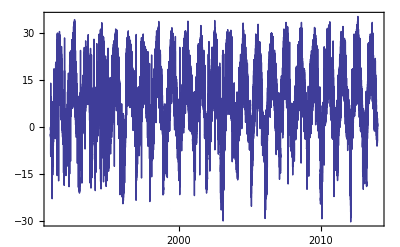

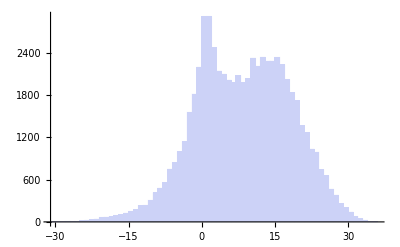

```mathematica
Tenviroment1=Interpolation@Transpose@{AbsoluteTime/@Temp1[[All,1]]-AbsoluteTime@StartTime,Temp1[[All,2]]};
DateListPlot[Temp1,Joined->True]
Histogram[Temp1[[All,2]]]
```

Humidity and Preciption

Chemical properties of air

## Architecture 1

Geometry parameters

Geometry of greenhause is characterized by 6 parameters - param[i], where i=OverBar[1,6]:

```mathematica
param[1]=612/100; param[2]=366/100; param[3]=320/100; param[4]=6/10; param[5]=1.2; param[6]=2;
Eparam[0]={0,0,0};Eparam[1]={param[1],0,0}; Eparam[2]={0,param[2],0};Eparam[3]={0,0,param[3]}; Eparam[4]={0,0,param[4]}; Eparam[5]={0,0,param[5]}; Eparam[6]={0,0,param[6]};
Agh=Eparam[0]; Bgh=Eparam[1];Cgh=Eparam[2]; Dgh= Eparam[3]; Egh=Eparam[4]+Eparam[2]; Fgh=Eparam[6]; Ggh= Eparam[2]+Eparam[4]+Eparam[5];  Hgh=Eparam[1]+Eparam[3]; Jgh=Eparam[2]+Eparam[1];  Kgh=Eparam[2]+Eparam[1]+Eparam[4] ;Lgh=Eparam[2]+Eparam[1]+Eparam[4]+Eparam[5];  Mgh=Eparam[1]+Eparam[6];
(*Square vectors*)
Vtop=param[1]{0,(param[3]-param[4]-param[5]),param[2]};
Vfront=param[1]param[5]{0,1,0};
Vside=(param[3]-param[6]+param[5])/2 param[3]{-1,0,0};
GreenHouse={LightGray,EdgeForm[Thick],
Map[Polygon[#]&,{{Agh,Bgh,Jgh,Cgh},{Cgh,Egh,Kgh,Jgh},{Agh,Dgh,Hgh,Bgh},{Agh,Fgh,Egh,Cgh}, {Mgh,Bgh,Jgh,Kgh}}],Blue,Opacity[1],
Map[Polygon[#]&,{{Dgh,Ggh,Lgh,Hgh},{Dgh,Ggh,Egh,Fgh},{Hgh,Mgh,Kgh,Lgh}, {Egh,Kgh,Lgh,Ggh}}],Gray,Map[Text[#[[1]],#[[2]],BaseStyle->{30}]&,{{"A",Agh},{"B",Bgh},{"C",Cgh},{"D",Dgh},{"E",Egh},{"F",Fgh},{"G",Ggh},{"H",Hgh},{"J",Jgh},{"K",Kgh},{"L",Lgh},{"M",Mgh}}],Yellow, Arrow[{(Hgh+Lgh+Ggh+Dgh)/4,(Hgh+Lgh+Ggh+Dgh)/4+Vtop/ Norm[Vtop]}],Arrow[{(Lgh+Kgh+Egh+Ggh)/4,(Lgh+Kgh+Egh+Ggh)/4+{0,1,0}}],Arrow[{(Ggh+Egh+Fgh+Dgh)/4,(Ggh+Egh+Fgh+Dgh)/4+{-1,0,0}}],Arrow[{(Hgh+Mgh+Lgh+Kgh)/4,(Hgh+Mgh+Lgh+Kgh)/4+{1,0,0}}]};
GeomInfo={{"Volume",Volume=param[1]param[2](param[3]+param[4]+param[5])/2},{"S_LHDG",Slhdg=Norm[Ggh-Dgh]param[1]},{"S_GDFE S_LHMK",Sgdfe=(param[3]-param[6]+param[5])/2 param[3]},{"S_LKEG",Slkeg=param[1]param[5]},{"S_KECJ",Skecj=param[1]param[4]},{"S_ABHD",Sabhd=param[1]param[3]},{"S_ACEF S_BMKJ",Sacef=(param[6]+param[4])/2 param[2]},{"S_ABJC", Sabjc=param[1]param[2]},{"S_KJCE",Skjce=param[1]param[4]},{"S_top",Stop=Norm[Ggh-Dgh]param[2]+(param[3]-param[6]+param[5])param[3]+param[1]param[5]},{"S_SIDE",Sside=param[1](param[4]+param[3])+(param[6]+param[4])param[2]},{"S_BOTTOM",Sbottom=param[1]param[2]},{"L_DG",Ldg=Norm[Ggh-Dgh]},{"L_EF",Lef=Norm[Egh-Fgh]}};
```

```mathematica
Graphics3D[GreenHouse,Axes->True,AxesLabel->{X,Y,Z}] 
Grid@GeomInfo//N
```

-Graphics3D-

Volume | 55.998
S_LHDG | 23.982
S_GDFE S_LHMK | 3.84
S_LKEG | 7.344
S_KECJ | 3.672
S_ABHD | 19.584
S_ACEF S_BMKJ | 4.758
S_ABJC | 22.3992
S_KJCE | 3.672
S_top | 29.3662
S_SIDE | 32.772
S_BOTTOM | 22.3992
L_DG | 3.91862
L_EF | 3.91862

Physical parameters

Light and Heat transmition parameters:
αwin - heat transmision coefficient of window 
and αwall - heat transmission cefficient of sides and bottom.
Rlight - light transmission coefficient it’s a fuction of angel betwen surface and solar radiation direction vectors.

Heat transmission coefficient of 2-glass - 1.6129 - 3.125 Wt/(m^2 K)
Heat transmission coefficient of wall - 0.34 - 0.5 Wt/(m^2 K)

```mathematica
αwin=18/10; αwall=4/10; αabsorb=1/10;
```

```mathematica
DeltaT=Tmicro[#]-Tenviroment1[#]&;
```

Ligh energy

Some avarage temperature going through surface of windows and some maximum (optimal) temeperature

```mathematica
SunSumPower = Compile[{{t,_Real}},Vfront.SunDirPower[t] HeavisideTheta[Vfront.SunDirPower[t]] + Vtop.SunDirPower[t] HeavisideTheta[Vtop.SunDirPower[t]] + Abs[Vside.SunDirPower[t]] ];
MaxSunSumPower = Compile[{{t,_Real}},Vfront.MaxSunDirPower[t] HeavisideTheta[Vfront.MaxSunDirPower[t]] + Vtop.MaxSunDirPower[t] HeavisideTheta[Vtop.MaxSunDirPower[t]] + Abs[Vside.MaxSunDirPower[t]] ];
```

Compile::cplist: R[Compile`FunctionVariable$566083] should be a tensor of type Integer, Real, or Complex; evaluation will use the uncompiled function.

Compile::cplist: Rmax[Compile`FunctionVariable$566255] should be a tensor of type Integer, Real, or Complex; evaluation will use the uncompiled function.

Temperature

Some optimal temperature function

```mathematica
Tmicro=19+3Sin[(2Pi #)/86400-Pi/2]&; Tenviroment1[t];
```

Humidity

```mathematica
Hum=65/100;
```

Chemical

## Power System

Mechanical energy

Light energy

```mathematica
Manipulate[Plot[{SunSumPower[t],MaxSunSumPower[t]},{t,α,α+β}],{{α,0},0,DeltaTime/10},{{β,80000},0,DeltaTime/10}]
```

Max power per year

```mathematica
MaxEnergyPerYear=2 365 NIntegrate[MaxSunSumPower[t],{t,0,43200}]
```

CompiledFunction::cfsa: Argument t at position 1 should be a "machine-size real number".

$Aborted[]

Heat energy

```mathematica
P = ((Stop αwin + (Sside + Sbottom) αwall) DeltaT[#] - αabsorb MaxSunSumPower[#]) HeavisideTheta[(Stop αwin + (Sside + Sbottom) αwall) DeltaT[#] - αabsorb MaxSunSumPower[#]] &;
```

```mathematica
Mean[N@Sin[Table[i,{i,0,DeltaTime/100}]]]
```

2.6972×10^-7